```mathematica
f[x_]:=(1-α)*x^(α-2)*Exp[-(x^(α-1)-μ*e1)^2/(2*σ^2*e2)]/Sqrt[2*Pi*σ^2*e2];
g[x_]:=f[x]/((1-α)*x^(α-2)-μ/S)^2;
```

```mathematica
α=3/4;
μ=1;
σ=.05;
e1=1.0053130689791008;
e2=1.0555293092628675;
S=100;
xcrit=(μ/(S*(1-α)))^(1/(α-2));
ϵ = 10^(-2);
```

General::munfl: Exp[-1.99511×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.27606×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8.1606×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

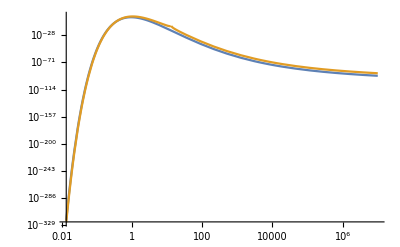

```mathematica
LogLogPlot[{f[x],g[x]},{x,.000000000001,10^7}, PlotRange->All]
```

```mathematica
NIntegrate[g[x],{x,0.1,10000}]
```

20.3306

```mathematica
NIntegrate[g[x],{x,0.1,xcrit-ϵ}]+NIntegrate[g[x],{x,xcrit+ϵ,10^4}]-2f[xcrit]/ϵ
```

20.3306

```mathematica
f[xcrit]/ϵ
```

8.71634×10^-16

```mathematica
g[xcrit+10^-10]
```

235772.

```mathematica
NIntegrate[f[x]*x^2,{x,0,10^21}]
```

5.81442×10^-50

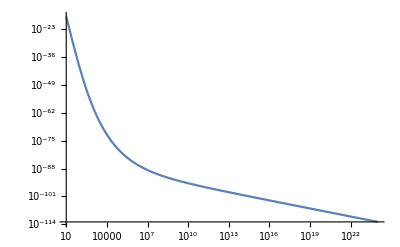

```mathematica
LogLogPlot[f[x],{x,10,1000000000000000000000000},PlotRange->All]
```

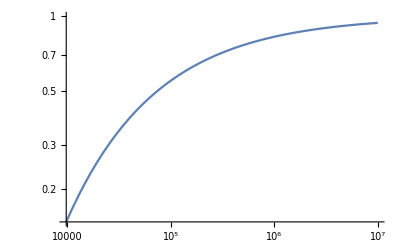

```mathematica
LogLogPlot[Exp[-x^(-1/2)/(2*σ^2*e2)],{x,0,10000000}]
```

```mathematica
NIntegrate[x^(-5/4)*Exp[-x^(-1/2)]*x,{x,0,1000}]
```

218.982

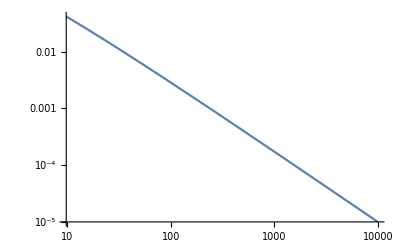

```mathematica
LogLogPlot[x^(-5/4)*Exp[-x^(-1/2)],{x,0,10000}]
```